```mathematica
"Plot ticks for direction and frequency";
dticks=Table[{(l-1)*90-180,Style[ToString[(l-1)*90-180],19],{0,.01}},{l,1,5}];
fticks=Table[{l*fmin,Style[ToString[l*fmin],19],{0,.01}},{l,1,7}];
```

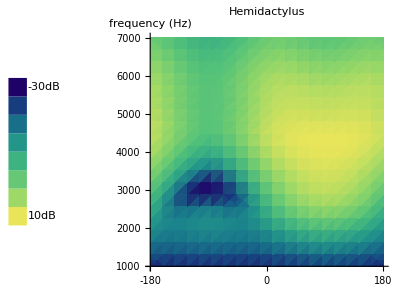

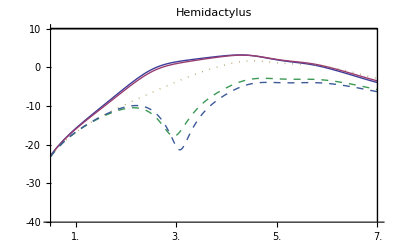

```mathematica
"Density Plot of Membrane Vibration Amplitude";
ShowLegend[DensityPlot[20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)],{θ,-180,180},{f,fmin,fmax},ColorFunction->"BlueGreenYellow",PlotPoints->20,Frame->False,Axes->True,AxesOrigin->{-180,fmin},AxesLabel->{None,Style["frequency (Hz)",14]},Ticks->{dticks,fticks},PlotLabel->Style[Speciesname,16],FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,8,"-30dB"," 10dB",LegendPosition->{-1.7,-.65},LegendOrientation->Vertical,LegendSize->1.25}]
```

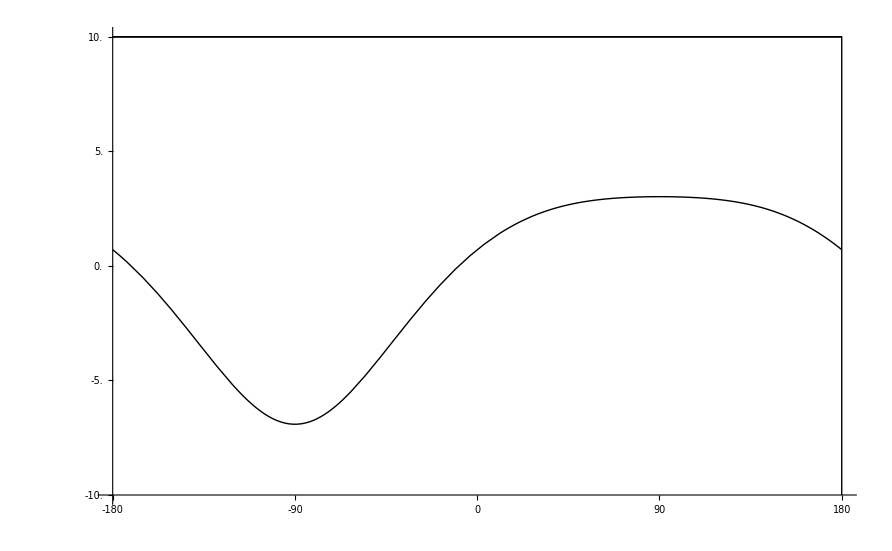

```mathematica
ftest=4000; "Test Frequency - refer Chapter 3 for values";
mrange=Round[-5+20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.{f->ftest,θ->-90},10];
prange=Round[5+20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.{f->ftest,θ->90},10];
ndbticks=5;
dbticks=Table[{(l-1)*(prange-mrange)/(ndbticks-1)+mrange,Style[ToString[N[(l-1)*(prange-mrange)/(ndbticks-1)+mrange]],18],{0,.005}},{l,1,ndbticks}];
dticks=Table[{(l-1)*90-180,Style[ToString[(l-1)*90-180],18],{0,.01}},{l,1,5}];
Plot[20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.f->ftest,{θ,-180,180},PlotRange->{mrange,prange},PlotStyle->Black,AxesOrigin->{-180,mrange},Ticks->{dticks,dbticks},Epilog->{Line[{{180,mrange},{180,prange},{-180,prange},{180,prange}}]}]
```

```mathematica
Style["-20 dB",15]
```

-20 dB

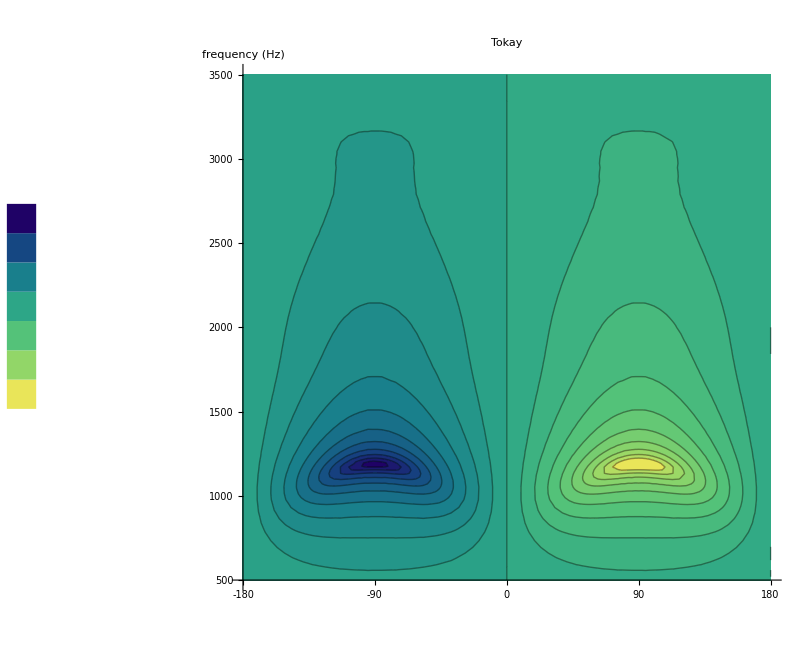

```mathematica
range=17+20*Log10[Abs[S0/SL]]/.{f->f0,θ->90};
ShowLegend[ContourPlot[20*Log10[Abs[S0/SL]],{θ,-180,180},{f,fmin,fmax},ColorFunction->"BlueGreenYellow",PlotPoints->20,Contours->20,Frame->False,Axes->True,PlotRange->range,AxesOrigin->{-180,fmin},AxesLabel->{None,Style["frequency (Hz)",15]},Ticks->{dticks,fticks},PlotLabel->Style[Speciesname,22],FrameLabel->{"direction(degrees)",None}],{ColorData["BlueGreenYellow"][#1]&,7,"","",LegendPosition->{-1.5,-.35},LegendOrientation->Vertical}]
```

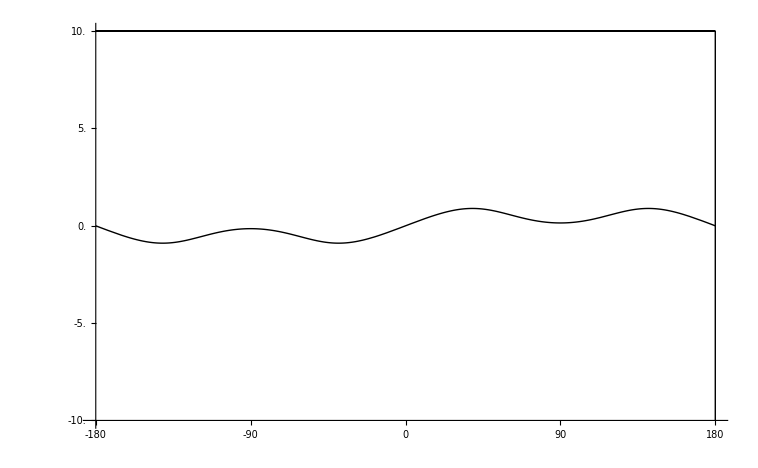

```mathematica
ftest=5000; "Test Frequency - refer Chapter 3 for values";
mrange=Round[-5+20*Log10[Abs[S0/SL]]/.{f->ftest,θ->-90},10];
prange=Round[5+20*Log10[Abs[S0/SL]]/.{f->ftest,θ->90},10];
ndbticks=5;
dbticks=Table[{(l-1)*(prange-mrange)/(ndbticks-1)+mrange,Style[ToString[N[(l-1)*(prange-mrange)/(ndbticks-1)+mrange]],18],{0,.005}},{l,1,ndbticks}];
Plot[20*Log10[Abs[S0/SL]]/.f->ftest,{θ,-180,180},PlotRange->{mrange,prange},PlotStyle->Black,AxesOrigin->{-180,mrange},Ticks->{dticks,dbticks},Epilog->{Line[{{180,mrange},{180,prange},{-180,prange},{180,prange}}]}]
```

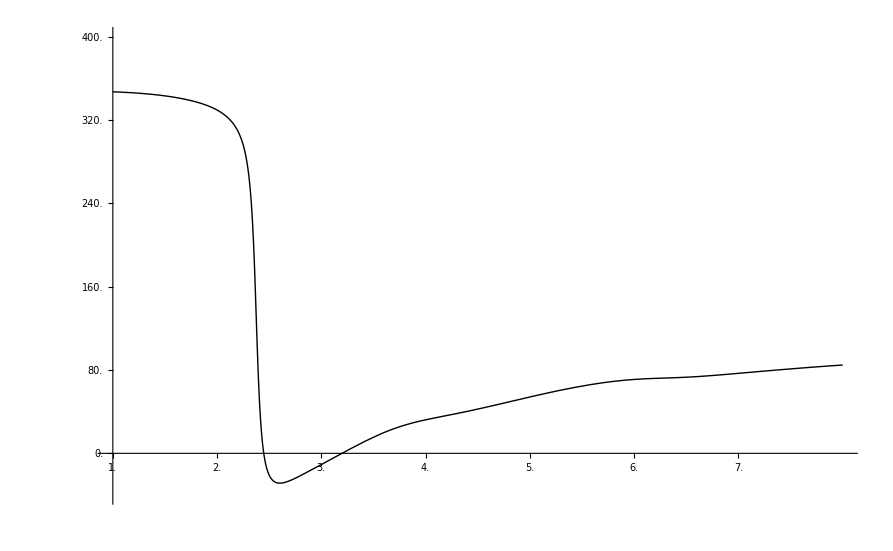

```mathematica
Tmax=Round[6*L*10^6/c,50];
ntticks=6;
tticks=Table[{(l-1)*Tmax/(ntticks-1),Style[ToString[N[(l-1)*Tmax/(ntticks-1)]],17],{0,.005}},{l,1,ntticks}];
fticks=Table[{l*fmin,Style[ToString[N[l]],17],{0,.01}},{l,1,7}];
Plot[{10^6*Arg[S0/SL]/ω/.θ->90},{f,fmin,fmax+500},PlotRange->{-40,Tmax},AxesOrigin->{fmin,0},Ticks->{fticks,tticks},PlotRange->All,PlotStyle->Black]
```

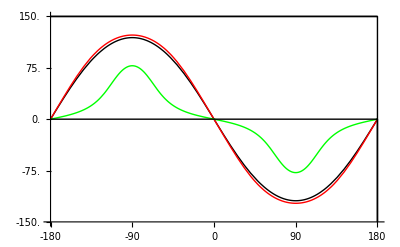

```mathematica
"iTD direction dependence";
ftest1=1000;
ntticks=5;
tticks=Table[{-Tmax+2*(l-1)*Tmax/(ntticks-1),Style[ToString[N[-Tmax+2*(l-1)*Tmax/(ntticks-1)]],17],{0,.005}},{l,1,ntticks}];
Plot[{10^6*Arg[SL/S0]/ω/.f->ftest1,10^6*Arg[SL/S0]/ω/.f->2*ftest1,10^6*Arg[SL/S0]/ω/.f->3*ftest1},{θ,-180,180},PlotRange->Tmax,PlotStyle->{Black,Red,Green},AxesOrigin->{-180,-Tmax},Ticks->{dticks,tticks},Epilog->{Line[{{-180,0},{180,0},{180,-Tmax},{180,Tmax},{-180,Tmax},{180,Tmax}}]},PlotLegend->{Style[".5kHz",Black,18],Style["1kHz",Black,18],Style["2kHz",Black,18]},LegendPosition->{-2.0,-.35}]
```

```mathematica
hemiiLD=iLD;
hemiiTD=iTD;
```

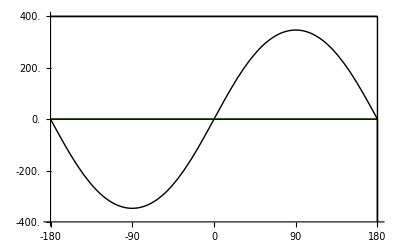

```mathematica
Tmax=400;
ftest1=1000;
ntticks=5;
tticks=Table[{-Tmax+2*(l-1)*Tmax/(ntticks-1),Style[ToString[N[-Tmax+2*(l-1)*Tmax/(ntticks-1)]],17],{0,.005}},{l,1,ntticks}];
Plot[{10^6*tokyiTD/.f->500,10^6*tokyiTD/ω/.f->1000,10^6*tokyiTD/ω/.f->2000},{θ,-180,180},PlotRange->Tmax,PlotStyle->{Black,Red,Green},AxesOrigin->{-180,-Tmax},Ticks->{dticks,tticks},Epilog->{Line[{{-180,0},{180,0},{180,-Tmax},{180,Tmax},{-180,Tmax},{180,Tmax}}]},PlotLegend->{Style[".5 kHz",Black,18],Style["1 kHz",Black,18],Style["2 kHz",Black,18]},LegendPosition->{-1.75,-.25}]
```

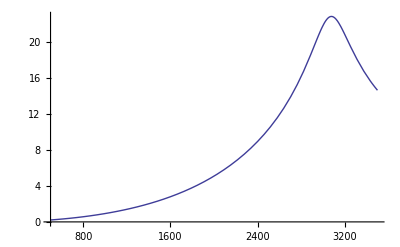

```mathematica
Plot[hemiiLD/.θ->90,{f,500,3500}]
```

```mathematica
dbticks=Table[{l*10-5,Style[ToString[l*10-5],18],{0,.005}},{l,1,4}]
fticks=Table[{l*1000,Style[ToString[l],18],{0,.01}},{l,1,7}];
GraphicsRow[{Plot[{If[1643.682≤f≤6505.03,3],hemiiLD/.θ->90,If[542.35≤f≤3238.11,3],iLD/.θ->90},{f,500,7000},PlotRange->{{500,7000.1},{0,40}},PlotStyle->{None,Black,None,Red},Ticks->{fticks,dbticks,None,None},AxesOrigin->{500,0},Filling->{2->{1},4->{3}},Epilog->{Line[{{500,40},{7000,40},{7000,0},{7000,40}}]}],Graphics[Legend[{{Graphics[{Black,Line[{{0,0},{1,0}}]}],Style["Hemidactylus",16]},{Graphics[{Red,Line[{{0,0},{1,0}}]}],Style["Tokay",16]}}]],Graphics[{Text[Style["frequency (kHz)",Medium]]}]}]
```

{{5,5,{0,0.005}},{15,15,{0,0.005}},{25,25,{0,0.005}},{35,35,{0,0.005}}}

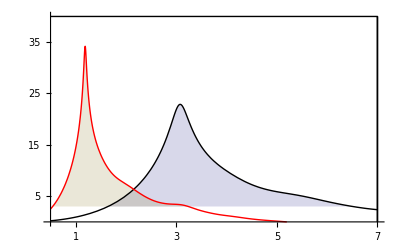

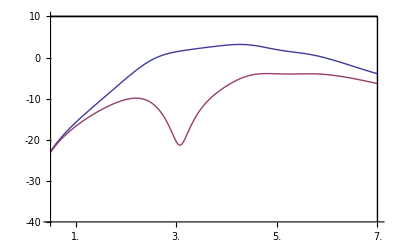

```mathematica
nlim=7;
dbticks=Table[{(l-1)*10-40,Style[ToString[(l-1)*10-40],22],{0,.005}},{l,1,6}];
fticks=Table[{l*1000,Style[ToString[N[l]],22],{0,.01}},{l,1,nlim}];Plot[{20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.θ->90,20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.θ->-90},{f,500,1000*nlim},PlotRange->{-40,10},PlotStyle->{ColorData[1][1],ColorData[1][2],Dotted,Dashed,Dashed},AxesOrigin->{500,-40},Epilog->{Line[{{1000*nlim,-40},{1000*nlim,10},{500,10},{1000*nlim,10}}]},Ticks->{fticks,dbticks},PlotLegend->{Style["   90°",23],Style["-90°",23]},LegendPosition->{.9,-.4}]
```

```mathematica
Plot[{20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.θ->90,20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.θ->60,20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.θ->0,20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.θ->-60,20*Log10[ω*Abs[S0]/(Pi*acyl*acyl)]/.θ->-90},{f,500,1000*nlim},PlotRange->{-40,10},PlotStyle->{ColorData[1][1],ColorData[1][2],Dotted,Dashed,Dashed},AxesOrigin->{500,-40},PlotLabel->Style[Speciesname,24],Epilog->{Line[{{1000*nlim,-40},{1000*nlim,10},{500,10},{1000*nlim,10}}]},Ticks->{fticks,dbticks},PlotLegend->{Style["   90°",23],Style["   60°",23],Style["  0°",23],Style["-60°",23],Style["-90°",23]},LegendPosition->{.9,-.4}]
```

-Graphics-

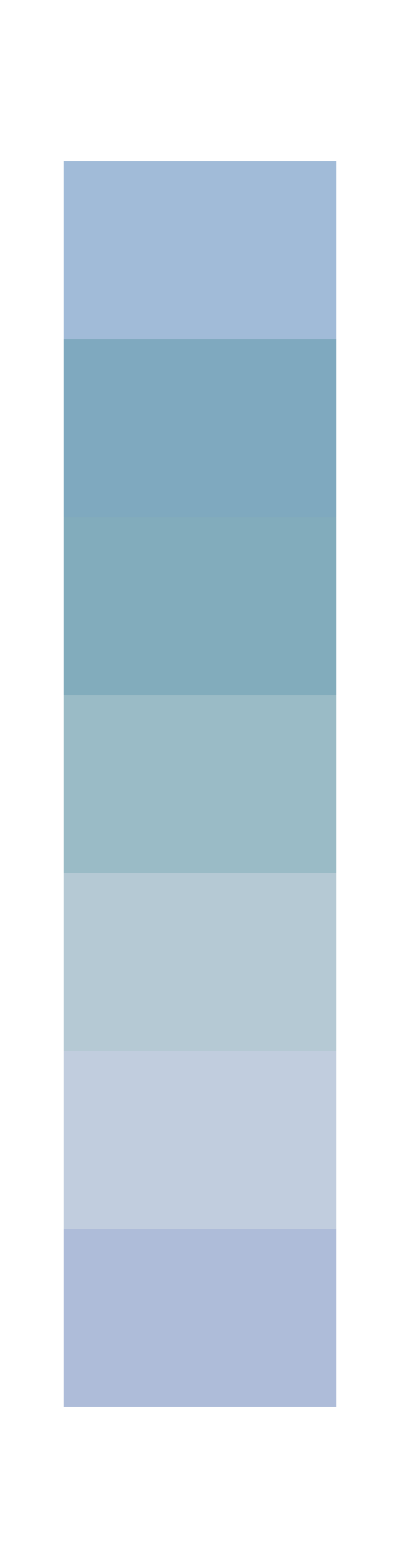

```mathematica
Graphics[Legend[ColorData["Aquamarine"][1-#1]&,7,"",""]]
```